```mathematica
(*формула Грегори*)
```

```mathematica
f[x_]:=ⅇ^(0.5x)
```

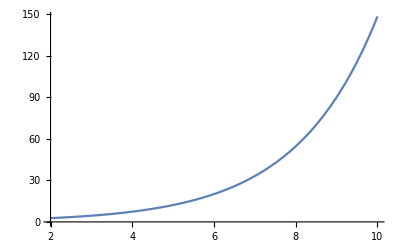

```mathematica
Plot[f[q],{q,2,10}]
```

```mathematica
Integrate[f[q],{q,4,8}]
```

94.4182

```mathematica
x=Range[4,8,0.001];
```

```mathematica
h=0.001;
n=Length@x-1;
```

```mathematica
n
```

4000

```mathematica
(*x - степень дельты, k - индекс y*)
```

```mathematica
delta[x_,k_]:=Sum[(-1)^(x-n)*Binomial[x,n]*y[[n+1+k]],{n,0,x}]
```

```mathematica
y=Table[f[x[[i]]],{i,1,Length@x}];
```

```mathematica
h(1/2 y[[1]]+1/2 y[[n]]+Sum[y[[i]],{i,2,n-1}])- h/12(delta[1,n-1]-delta[1,1])-h/24(delta[2,n-2]+delta[2,1])+ 19 h/720(delta[3,n-3]-delta[3,1])-3 h/160(delta[4,n-4]+delta[4,1])-836 h/60480(delta[5,n-5]-delta[5,1])-275 h/24192(delta[6,n-6]+delta[6,1])-33953 h/3628800(delta[7,n-7]-delta[7,1])
```

94.3636